```mathematica
R = {{1/10,4/10,5/10},{3/10,3/10,4/10},{1/10,1/10,8/10}};
rrr[n_] :=({1,0,0}.MatrixPower[R,n])[[3]]; (*start at 2, end at 3*)
```

```mathematica
Down here is not needed until...
```

Down here is needed not until...

```mathematica
(*a[n_] :=FullSimplify[rrr[n]]*)
```

```mathematica
(*s4[L_] :=Sum[Product[(1-a[i]),{i,r+1,L}]*a[r],{r,0,L}]*)
```

```mathematica
(*N[s4[1]] (* check if expected*)*)
```

```mathematica
(*N[s4[4]]*)
```

```mathematica
(*N[1-(2/3)^7]*)
```

```mathematica
(*DiscretePlot[{s4[n],1-(2/3)^n},{n,0,7}]*)
```

```mathematica
Now! this is needed below
```

below is needed this Fri 23 Jun 2023 16:48:23GMT+2!

```mathematica
gam = {g1,g2,g3};
rho0={r1,r2,r3};
rho[n_]:=rho0.MatrixPower[R,n];
sgen[n_] :=Sum[Product[(1-Sum[rho[h][[j]] gam[[j]],{j,1,3}]),{h,r+1,n}]*Sum[rho[r][[j]] gam[[j]],{j,1,3}],{r,1,n}] ;
```

```mathematica
s1[n_]:=sgen[n]/.{r1->1,r2->0,r3->0,g1->1/3,g2->1/3,g3->1/3};
s2[n_]:= sgen[n]/.{r1->1,r2->0,r3->0,g1->0,g2->0,g3->1};
s3[n_]:=sgen[n]/.{r1->1,r2->0,r3->0,g1->10/74,g2->13/74,g3->51/74};
s4[n_]:=sgen[n]/.{r1->1,r2->0,r3->0,g1->1/2,g2->1/4,g3->1/4};
```

```mathematica
(* total hack below for s5*)
gam0 = {g1,g2,g3};
Cop = R;
rho0={r1,r2,r3};
gam2[n_]:= gam0.MatrixPower[Cop,n];
rho[n_]:=rho0.MatrixPower[R,n];
sgen2[n_] :=Sum[Product[(1-Sum[rho[h][[j]] gam2[h][[j]],{j,1,3}]),{h,r+1,n}]*Sum[rho[r][[j]] gam2[r][[j]],{j,1,3}],{r,1,n}] ;
(* CHANGE THE R1,2,3 AND G1,2,3 BELOW FOR MARKOV STUFF *)
s5[n_]:=sgen2[n]/.{r1->0,r2->1,r3->0,g1->1,g2->0,g3->0};
```

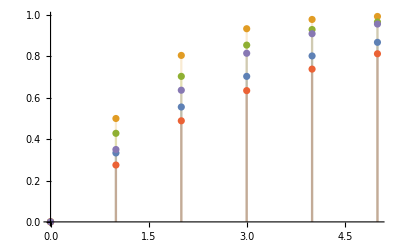

0

```mathematica
DiscretePlot[{s1[n],s2[n],s3[n],s4[n],s5[n]},{n,0,5}]
```